# Quantum Oracle: Properties

This  is  a demonstration material accompanying the corresponding YouTube video.

Episode 26. Classical Oracle

Episode 27. Quantum Oracle: Definition

Episode 28. Quantum Oracle: Properties

NOTICE: This notebook has been updated after the YouTube video was taken.

## Preliminary

Here, let us set up classical and quantum oracles to be used in the examples below.

```mathematica
$m=3;
$n=2;
```

```mathematica
f[1]=f[2]=3;
f[7]=2;
f[_Integer]=0;
```

```mathematica
ff=Oracle[f,$m,$n];
xx=Tuples[{0,1},$m];
yy=ff/@xx;
```

```mathematica
Thread[xx->yy]//TableForm
```

```mathematica
Let[Qubit,S,T]
```

```mathematica
SS=S[Range[$m],$];
TT=T[Range[$n],$];
```

```mathematica
op=Oracle[f,SS,TT]
```

```mathematica
qc=QuantumCircuit[op]
```

## Making Copies

The CNOT gate makes a copy of the computational basis state of the control register to the target register when the latter has been prepared initially in the state 0,

x⊗0↦x⊗x.

The quantum oracle has a similar property, but it makes a copy of the image f(x) rather than the input state x itself of the native register to the ancillary register,

x⊗0↦x⊗f(x).

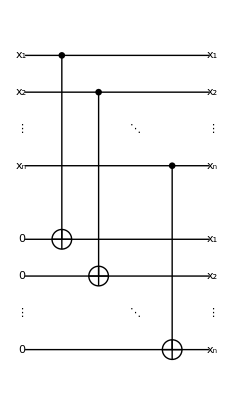
-Graphics-	                -Graphics-

Figure 4. (left) A quantum circuit demonstrating the feature x⊗0↦x⊗f(x) of the quantum oracle corresponding to classical oracle f:{0,1}^m→{0,1}^n. (right) A quantum circuit demonstrating the feature x⊗0↦x⊗x of the CNOT gates.

### Example

```mathematica
QuantumCircuit[Ket[TT],op]
```

```mathematica
in=Basis[SS];
ProductForm[in,{SS,TT}]
```

```mathematica
out=op**in;
ProductForm[out,{SS,TT}]
```

```mathematica
ProductForm[Thread[in->out],{SS,TT}]//TableForm
```

```mathematica
Thread[xx->yy]//TableForm
```

### Superposition State

Furthermore, suppose that a native quantum register is in the superposition

1/2^(m/2)Σ_(x=0)^(2^m-1)x

and the ancillary quantum register in in the state 0≡0^(⊗n). The quantum oracle transforms the state as

1/2^(m/2)Σ_(x=0)^(2^m-1)x⊗0↦1/2^(m/2)Σ_(x=0)^(2^m-1)x⊗f(x)

Just like the CNOT gate, the above state from the quantum oracle is also entangled in general unless f is a constant or very special function. In this case, the entanglement is controlled by the (classical) oracle f.

```mathematica
QuantumCircuit[Ket[TT],op]
```

```mathematica
in=Total@Basis[SS];
ProductForm[in,{SS,TT}]
```

```mathematica
out=op**in;
ProductForm[out,{SS,TT}]
```

```mathematica
Thread[xx->yy]//TableForm
```

## Marking

The controlled-unitary gate induces a phase shift on the control register (rather than on the target register) when the target register is in an eigenstate of the unitary operator.

A similar method can be used to induce a phase shift conditionally on every term that satisfies a certain condition:

x↦(x(-1))^(f(x))

More generally,

Σ_(x=0)^(2^n-1)x  ↦  Σ_(x=0)^(2^n-1)(x(-1))^(f(x))

-Graphics-                 -Graphics-

Figure 5. (left) A quantum circuit to induces conditional phase shifts depending on function value f(x) at input value x:=(x_1,x_2,…,x_n). (right) For comparison, the controlled exponentiation of a unitary gate induces an x-dependent phase shift, where x:=(x_1 x_2(…x)_m)_2.

### Example

```mathematica
QuantumCircuit[ProductState[T[{1,2}]->{1,-1},"Label"->{Ket@{"+"},Ket@{"-"}}],op]
```

```mathematica
in=Basis[SS]**ProductState[T[1]->{1,1},T[2]->{1,-1}];
KetFactor[in]
```

```mathematica
out=op**in;
KetFactor[out]
```

```mathematica
Thread[KetFactor[in]->KetFactor[out]]//TableForm
```

```mathematica
Thread[xx->yy]//TableForm
```

### Superposition State

```mathematica
QuantumCircuit[ProductState[T[{1,2}]->{1,-1},"Label"->{Ket@{"+"},Ket@{"-"}}],op]
```

```mathematica
in=Total@Basis[SS]**ProductState[T[1]->{1,1},T[2]->{1,-1}];
KetFactor[in]
```

```mathematica
out=op**in;
ProductForm[out,{SS,TT}]
```

```mathematica
KetFactor[out]
```

```mathematica
Thread[xx->yy]//TableForm
```

## Summary

### Keywords

Oracle

Quantum oracle

Quantum decision making

### Functions

Oracle

ControlledExp

### Related Links

Section 4.2 of the Quantum Workbook (2022, 2023).

Tutorial: Quantum Oracle

Tutorial: Quantum Decision Algorithms

Full List of Demonstrations in YouTube Videos

## Epilogue